```mathematica
SetDirectory[NotebookDirectory[]]
length=12.0;
ks=(3 π)/2;
M2=3;
M3=3;
ν1=2;
ν2=0.1;
g=980;
σ=72;
ρ=1;
mat1[s_,k_,ω_,As_,ks_,height_]:=ArrayFlatten[Table[Exp[-(k+n*ks)*height]/(Exp[k*height]+Exp[-k*height])*((-ω^2*(s+m)^2+I*ω*(s+m)*(ν1+(k+n*ks)^2*ν2))-(g+σ/ρ*(k+n*ks)^2)*(k+n*ks))*KroneckerDelta[m,o]*(BesselJ[n-l,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l-1,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l+1,I*(k+n*ks)*As])+Exp[(k+n*ks)*height]/(Exp[k*height]+Exp[-k*height])*(-ω^2*(s+m)^2+I*ω*(s+m)*(ν1+(k+n*ks)^2*ν2)+(g+σ/ρ*(k+n*ks)^2)*(k+n*ks))*KroneckerDelta[m,o]*(BesselJ[n-l,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l-1,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l+1,-I*(k+n*ks)*As]),{n,-M2,M2},{l,-M2,M2},{m,-M3,M3},{o,-M3,M3}]];
mat2[s_,k_,ω_,As_,ks_,height_]:=ArrayFlatten[Table[Exp[-(k+n*ks)*height]/(Exp[k*height]+Exp[-k*height])*(ω^2*(k+n*ks)/2)*(KroneckerDelta[m,o+1]+KroneckerDelta[m,o-1])*(BesselJ[n-l,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l-1,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l+1,I*(k+n*ks)*As])+Exp[(k+n*ks)*height]/(Exp[k*height]+Exp[-k*height])*(-ω^2*(k+n*ks)/2)*(KroneckerDelta[m,o+1]+KroneckerDelta[m,o-1])*(BesselJ[n-l,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l-1,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l+1,-I*(k+n*ks)*As]),{n,-M2,M2},{l,-M2,M2},{m,-M3,M3},{o,-M3,M3}]]
mat3[s_,k_,ω_,height_]:=ArrayFlatten[Table[((-ω^2*(s+m)^2+I*ω*(s+m)*(ν1+k^2*ν2))+Tanh[k*height]*(g+σ/ρ*k^2)*k)*KroneckerDelta[m,o],{m,-M3,M3},{o,-M3,M3}]];
mat4[s_,k_,ω_,height_]:=ArrayFlatten[Table[-Tanh[k*height]*(ω^2*k/2)*(KroneckerDelta[m,o+1]+KroneckerDelta[m,o-1]),{m,-M3,M3},{o,-M3,M3}]]
```

/home/zack/oscillators/faraday

### Harmonic and subharmonic tongues

{13.5758,Null}

{9.96807,Null}

{30.7024,Null}

{30.0029,Null}

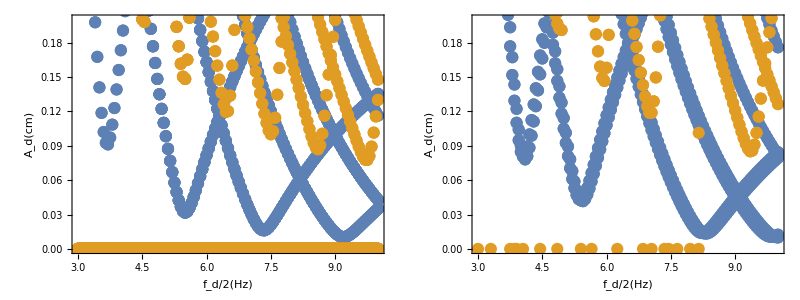

```mathematica
ω1=2*Pi*6;
ω2=2*Pi*20;
dω=2*Pi*0.1;
kmin=0;
kmax=2*Pi/length*6;
height=0.5;
AbsoluteTiming[vals1=DeleteCases[Flatten[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.5,k,ω,0.0,ks,height],mat2[0.5,k,ω,0.0,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω},{k,kmin,kmax,2*Pi/length}],1],{}];]
AbsoluteTiming[vals2=Flatten[DeleteCases[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.0,k,ω,0.0,ks,height],mat2[0.0,k,ω,0.0,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω},{k,kmin,kmax,2*Pi/length}],{}],1];]
As=0.8*height;
AbsoluteTiming[vals3=DeleteCases[Flatten[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.5,k,ω,As,ks,height],mat2[0.5,k,ω,As,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω},{k,kmin,kmax,2*Pi/length}],1],{}];]
AbsoluteTiming[vals4=DeleteCases[Flatten[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.0,k,ω,As,ks,height],mat2[0.0,k,ω,As,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω},{k,kmin,kmax,2*Pi/length}],1],{}];]
p1=ListPlot[{Flatten[vals1,1],Flatten[vals2,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,0.2}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350];
p2=ListPlot[{Flatten[vals3,1],Flatten[vals4,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,0.2}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350];
Grid[{{p1,p2}}]
```

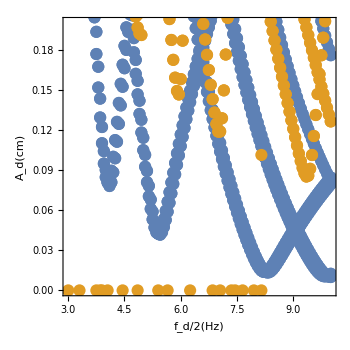

```mathematica
ListPlot[{Flatten[vals3,1],Flatten[vals4,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,0.2}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350]
```

```mathematica
2*(ks/2*Tanh[ks/2*height]*(g+σ/ρ*(ks/2)^2))^(1/2)/(2*Pi)
2*((ks/2-2*Pi/length)*Tanh[(ks/2-2*Pi/length)*height]*(g+σ/ρ*(ks/2-2*Pi/length)^2))^(1/2)/(2*Pi)
```

16.5031

12.8173

```mathematica
height=0.1;
(ks/2*Tanh[ks/2*height]*(g+σ/ρ*(ks/2)^2))^(1/2)/(2*Pi*2)
(ks*Tanh[ks*height]*(g+σ/ρ*(ks)^2))^(1/2)/(2*Pi*2)
```

2.18238

5.81376

{18.4685,Null}

{18.5801,Null}

{49.3112,Null}

{49.4792,Null}

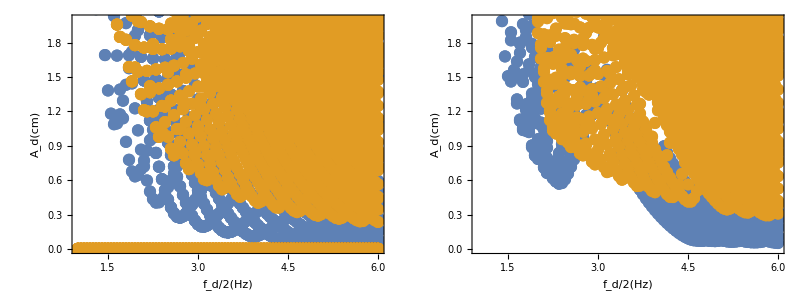

```mathematica
ω1=2*Pi*2;
ω2=2*Pi*12;
dω=2*Pi*0.1;
kmin=0;
kmax=2*Pi/length*16;
height=0.1;
AbsoluteTiming[vals1=DeleteCases[Flatten[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.5,k,ω,0.0,ks,height],mat2[0.5,k,ω,0.0,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω},{k,kmin,kmax,2*Pi/length}],1],{}];]
AbsoluteTiming[vals2=Flatten[DeleteCases[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.0,k,ω,0.0,ks,height],mat2[0.0,k,ω,0.0,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω},{k,kmin,kmax,2*Pi/length}],{}],1];]
As=0.9*height;
AbsoluteTiming[vals3=DeleteCases[Flatten[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.5,k,ω,As,ks,height],mat2[0.5,k,ω,As,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω},{k,kmin,kmax,2*Pi/length}],1],{}];]
AbsoluteTiming[vals4=DeleteCases[Flatten[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.0,k,ω,As,ks,height],mat2[0.0,k,ω,As,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω},{k,kmin,kmax,2*Pi/length}],1],{}];]
p1=ListPlot[{Flatten[vals1,1],Flatten[vals2,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,2}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350];
p2=ListPlot[{Flatten[vals3,1],Flatten[vals4,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,2}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350];
Grid[{{p1,p2}}]
```

### Compare with finite elements

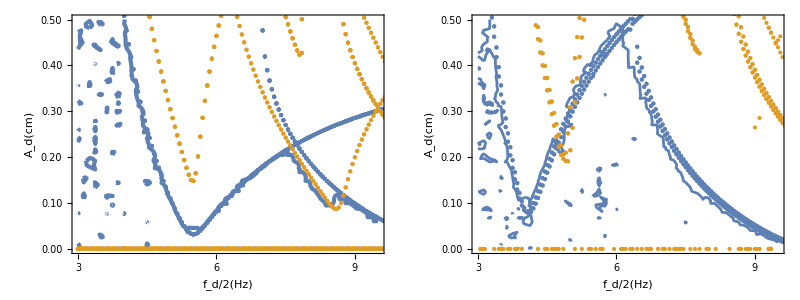

```mathematica
filebases={"sweeps/sharpamp/1001"};
cols={ColorData[97,"ColorList"][[1]]};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p1=Show[Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.0},PlotRange->{{3,9.5},{0,0.5}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[3]]},LabelStyle->Directive[16,Black], FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}],{i,1,Length[sweeps]}],ListPlot[{Flatten[vals1,1],Flatten[vals2,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,0.5}},PlotStyle->Directive[PointSize[0.01]],ImageSize->350]];
filebases={"sweeps/sharpamp/1003"};
cols={ColorData[97,"ColorList"][[1]]};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p2=Show[Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.0},PlotRange->{{3,9.5},{0,0.5}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black], FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}],{i,1,Length[sweeps]}],ListPlot[{Flatten[vals3,1],Flatten[vals4,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,0.5}},PlotStyle->Directive[PointSize[0.01]],ImageSize->350]];
Grid[{{p1,p2}}]
```

```mathematica
gap=2*Pi/length*3/2;
ks=2*gap;
height=0.5;
As=0.9*height;
dϵ=0.01;
ω=0.8*2*(gap*Tanh[height*gap]*(g+σ/ρ*gap^2))^(1/2);
ω/(2*Pi*2)
```

6.60123

### Frequency ratio sweep

{4.77883,Null}

{14.778,Null}

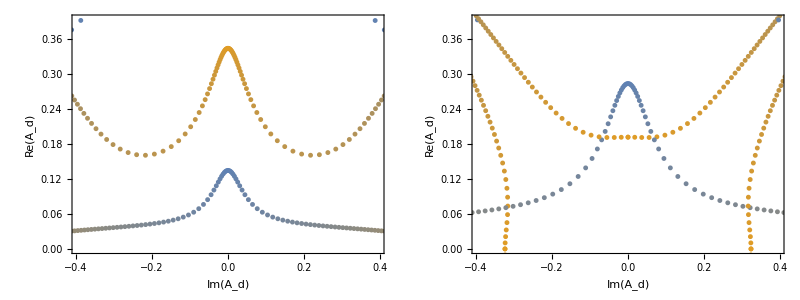

plots/eigenvalues.pdf

```mathematica
M2=3;
M3=5;
dϵ=0.005;
ω=2*Pi*9.8;
As=0.0;
AbsoluteTiming[vals1=ParallelTable[val=Eigenvalues[{mat1[ϵ,2*Pi/length,ω,As,ks],mat2[ϵ,2*Pi/length,ω,As,ks]}];{Im[#],Re[#]}&/@val,{ϵ,0,1.0,dϵ}];]
scale=3*Abs[(First@MinimalBy[Cases[Flatten[vals1,1],u_/;Abs[u[[1]]]<0.01],Abs[#[[2]]]&])[[2]]];
cols=Blend[{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]},#]&/@(2*Abs[(Range[Length[vals1]]-(Length[vals1]-1)/2-1)/(Length[vals1]-1)]);
p1=ListPlot[vals1,Joined->False,PlotRange->{{-scale,scale},{0,scale}},PlotStyle->(Directive[#,PointSize[0.01]]&/@cols),ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1];
As=0.4;
AbsoluteTiming[vals2=ParallelTable[val=Eigenvalues[{mat1[ϵ,2*Pi/length,ω,As,ks],mat2[ϵ,2*Pi/length,ω,As,ks]}];{Im[#],Re[#]}&/@val,{ϵ,0,1.0,dϵ}];]
cols=Blend[{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]},#]&/@(2*Abs[(Range[Length[vals1]]-(Length[vals1]-1)/2-1)/(Length[vals1]-1)]);
scale=3*Abs[(First@MinimalBy[Cases[Flatten[vals1,1],u_/;Abs[u[[1]]]<0.01],Abs[#[[2]]]&])[[2]]];
p2=ListPlot[vals2,Joined->False,PlotRange->{{-scale,scale},{0,scale}},PlotStyle->(Directive[#,PointSize[0.01]]&/@cols),ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1];
p=Grid[{{p1,p2}}]
Export["plots/eigenvalues.pdf",p]
```

43.8793

{6.67685,Null}

4.83545

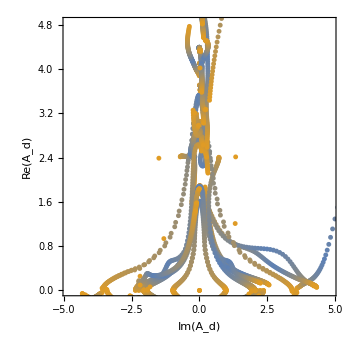

```mathematica
M2=3;
M3=3;
gap=2*Pi/length*3/2;
ks=2*gap;
height=0.1;
As=0.9*height;
dϵ=0.01;
ω=0.8*2*(gap*Tanh[height*gap]*(g+σ/ρ*gap^2))^(1/2)
AbsoluteTiming[vals2=Flatten[ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,As,ks],mat2[ϵ,k,ω,As,ks]}];{Im[#],Re[#]}&/@val,{ϵ,0,1.0,dϵ},{k,2*Pi/length,2*Pi/length*3,2*Pi/length}],1];]
cols=Blend[{ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]},#]&/@(2*Abs[(Range[Length[vals2]]-(Length[vals2]-1)/2-1)/(Length[vals2]-1)]);
scale=3*Abs[(First@MinimalBy[Cases[Flatten[vals2,1],u_/;Abs[u[[1]]]<10^-2&&Abs[u[[2]]]>0.1],Abs[#[[2]]]&])[[2]]]
p2=ListPlot[vals2,Joined->False,PlotRange->{{-scale,scale},{0,scale}},PlotStyle->(Directive[#,PointSize[0.01]]&/@cols),ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1]
```

### Plots

```mathematica
dω=2*Pi*0.05;
AbsoluteTiming[vals5=DeleteCases[ParallelTable[val1=Abs[Cases[Eigenvalues[{mat1[0.0,2*Pi/length,ω,0.4,ks],mat2[0.0,2*Pi/length,ω,0.4,ks]}],u_/;Abs[Im[u]]<10^-2]];val2=Abs[Cases[Eigenvalues[{mat1[0.5,2*Pi/length,ω,0.4,ks],mat2[0.0,2*Pi/length,ω,0.4,ks]}],u_/;Abs[Im[u]]<10^-2]];
val=Join[val1,val2];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{}];]
AbsoluteTiming[vals1=DeleteCases[ParallelTable[val1=Abs[Cases[Eigenvalues[{mat3[0.5,2*Pi/length,ω],mat4[0.5,2*Pi/length,ω]}],u_/;Abs[Im[u]]<10^-6]];
val2=Abs[Cases[Eigenvalues[{mat3[0.5,2*Pi/length*2,ω],mat4[0.5,2*Pi/length*2,ω]}],u_/;Abs[Im[u]]<10^-6]];val3=Abs[Cases[Eigenvalues[{mat3[0.0,2*Pi/length*3,ω],mat4[0.0,2*Pi/length*3,ω]}],u_/;Abs[Im[u]]<10^-6]];
val=Join[val1,val2,val3];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{}];]
```

{16.6074,Null}

{0.093006,Null}

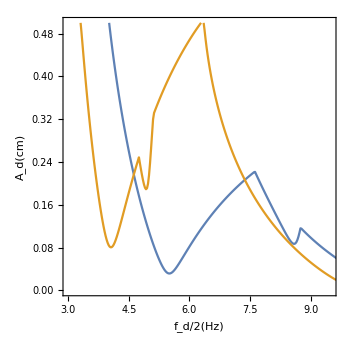

data/flatfloquet.txt

data/periodicfloquet.txt

```mathematica
ListPlot[{First@MinimalBy[#,#[[2]]&]&/@vals1,First@MinimalBy[#,#[[2]]&]&/@vals5},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->{{3,9.5},{0,0.5}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350]
Export["data/flatfloquet.txt",First@MinimalBy[#,#[[2]]&]&/@vals1,"Table"]
Export["data/periodicfloquet.txt",First@MinimalBy[#,#[[2]]&]&/@vals5,"Table"]
```